# Fresnel

```mathematica
<<"Labor`"
```

## Messung

### Laser auf 45° einstellen damit s und p Polaritierung gleich sind

### Optische Achse einrichten

### Justieren des Sschwenkarms ~90° zum festem Arm

### Messen der reflektierten intsensität

```mathematica
dI=0.01;
dα=0.1 Degree;
off= 0.006;
Ir={{"α/°", "I l-g p/V", "I l-g s/V", "I g-l p/V", "I g-l s/V"}, {10, 2, 0, 0, 0}, {15, 3, 0, 0, 0}, {20, 4, 0, 0, 0}, {25, 5, 0, 0, 0}, {30, 6, 0, 0, 0}, {35, 3, 0, 0, 0}, {40, 2, 0, 0, 0}, {45, 2, 0, 0, 0}, {50, 3, 0, 0, 0}, {55, □, □, □, □}, {60, □, □, □, □}, {65, □, □, □, □}, {70, □, □, □, □}, {75, □, □, □, □}, {80, □, □, □, □}, {85, □, □, □, □}, {90, □, □, □, □}};
```

### Normierung der Intensität

```mathematica
I0={{"I l-g/V", "I g-l/V"}, {10, 9}};
```

### Graphische Darstellung

```mathematica
pIs=Table[{Ir[[x,1]],(Ir[[x,2]]-off)/I0[[2,1]]},{x,2,Length[Ir]}];
pIp=Table[{Ir[[x,1]],(Ir[[x,3]]-off)/I0[[2,2]]},{x,2,Length[Ir]}];
```

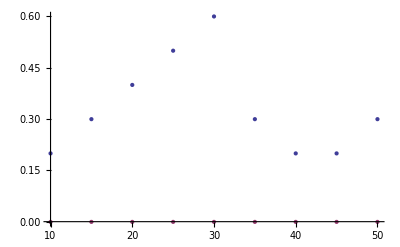

```mathematica
ListPlot[{pIs,pIp}]
```

### Berechnen der Brechzahl

```mathematica
n1=1;dn1=0;
α=43Degree;dα=0.1Degree;
n2=Optic`RefIndexTotal[n1,dn1,α,dα]//N
```

{1.46628,0.00274434}

### Berechnen der theoretischen p uns s Reflextion

```mathematica
ArcSin[(n1 Ir[[6,1]]Degree)/n2[[1]]]*180/π
```

20.9218

```mathematica
Ist=Table[Optic`Fresnel[n1,n2[[1]],Ir[[x,1]]Degree,ArcSin[(n1 Sin[Ir[[x,1]]Degree])/n2[[1]]],dn1,n2[[2]],dα,dα],{x,2,Length[Ir]}];
Ipt=Table[Optic`Fresnel[n2[[1]],n1,Ir[[x,1]]Degree,ArcSin[(n1 Sin[Ir[[x,1]]Degree])/n2[[1]]],n2[[2]],dn1,dα,dα],{x,2,Length[Ir]}];
```

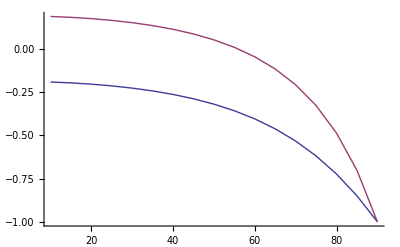

```mathematica
ListPlot[{
Table[{Ir[[x,1]],Ist[[x-1,1]]},{x,2,Length[Ir]}],
Table[{Ir[[x,1]],Ipt[[x-1,1]]},{x,2,Length[Ir]}]
},PlotRange->{{0,95},{1,-1.5}},Joined->True]
```